Dataset[<>]

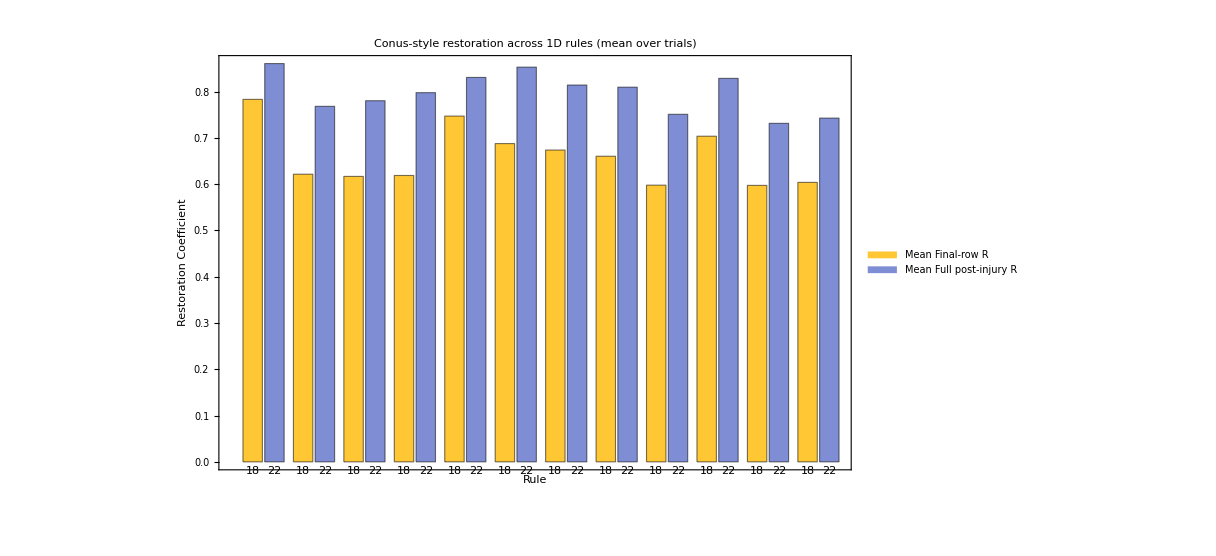

Dataset[<>]

No nontrivial rules passed the filter. Relax thresholds if needed.

All exports saved in: /Volumes/External/Ruliology/conus_repeated_trials_exports

```mathematica
ClearAll["Global`*"];

(* =========================================================1. USER PARAMETERS=========================================================*)

(*First pass rule set:classic+candidate shell-like rules*)
rulesToTest={18,22,30,45,54,60,73,90,105,110,126,150};

width=201;
steps=150;

injuryStep=40;
injuryRadius=8;

nTrials=20;
randomSeed=12345;

exportBase=FileNameJoin[{NotebookDirectory[],"conus_repeated_trials_exports"}];

SeedRandom[randomSeed];

If[!DirectoryQ[exportBase],CreateDirectory[exportBase]];

(* =========================================================2. HELPERS=========================================================*)

makeInitialState[w_Integer]:=Module[{init},init=ConstantArray[0,w];
init[[Ceiling[w/2]]]=1;
init];

injureState[state_List,radius_Integer,mode_:"RandomBinary"]:=Module[{center,injuryPositions,replacementValues},center=Ceiling[Length[state]/2];
injuryPositions=Select[Range[center-radius,center+radius],1<=#<=Length[state]&];
replacementValues=Switch[mode,"RandomBinary",RandomInteger[1,Length[injuryPositions]],"Delete",ConstantArray[0,Length[injuryPositions]],"Flip",1-state[[injuryPositions]],_,RandomInteger[1,Length[injuryPositions]]];
ReplacePart[state,Thread[injuryPositions->replacementValues]]];

restorationMetrics[controlEvo_,injuredFullEvo_,injStep_Integer]:=Module[{finalControl,finalInjured,xorFinal,Rfinal,controlPost,injuredPost,xorPost,Rfull},finalControl=controlEvo[[-1]];
finalInjured=injuredFullEvo[[-1]];
xorFinal=Mod[finalControl+finalInjured,2];
Rfinal=1-N[Total[xorFinal]/Length[xorFinal]];
controlPost=controlEvo[[injStep+1;;]];
injuredPost=injuredFullEvo[[injStep+1;;]];
xorPost=Mod[controlPost+injuredPost,2];
Rfull=1-N[Total[Flatten[xorPost]]/Length[Flatten[xorPost]]];
<|"FinalXOR"->xorFinal,"PostXOR"->xorPost,"Rfinal"->Rfinal,"Rfull"->Rfull|>];

patternDensity[evo_]:=N[Mean[Flatten[evo]]];

rowEntropy[row_List]:=Module[{p},p=N[Counts[row]/Length[row]];
-Total[Values[p]*Log2[Values[p]+10^-12]]];

meanEntropy[evo_]:=Mean[rowEntropy/@evo];

adjacencyVariation[evo_]:=Mean[Table[Mean[Boole[Differences[evo[[i]]]!=0]],{i,Length[evo]}]];

classifyRule[evo_,rfull_,density_,entropy_,variation_]:=Which[density<0.02,"Trivial sparse",density>0.98,"Trivial full",entropy<0.15&&variation<0.05,"Simple periodic",entropy>0.80&&variation>0.45&&rfull<0.75,"Chaotic fragile",entropy>0.45&&variation>0.15&&rfull>=0.75,"Structured robust",variation>0.10&&variation<0.35,"Fractal / nested",True,"Mixed / intermediate"];

plotControl[evo_,rule_]:=ArrayPlot[evo,ColorRules->{0->White,1->Black},Frame->True,Mesh->False,PlotLabel->Style["A. Control growth (Rule "<>ToString[rule]<>")",13,Bold],ImageSize->320];

plotInjured[evo_,rule_,injStep_]:=Show[ArrayPlot[evo,ColorRules->{0->White,1->Black},Frame->True,Mesh->False,PlotLabel->Style["B. Injured growth (Rule "<>ToString[rule]<>")",13,Bold],ImageSize->320],Graphics[{{Red,Thick,Dashed,Line[{{0.5,injStep+1.5},{Length[evo[[1]]]+0.5,injStep+1.5}}]}}]];

plotFinalXOR[xorRow_,rVal_,rule_]:=ArrayPlot[{xorRow},ColorRules->{0->White,1->Red},Frame->True,Mesh->False,PlotLabel->Style["C. Final XOR (Rule "<>ToString[rule]<>", R = "<>ToString[NumberForm[rVal,{3,3}]]<>")",13,Bold],ImageSize->320];

plotPostXOR[xorPost_,rVal_,rule_]:=ArrayPlot[xorPost,ColorRules->{0->White,1->Red},Frame->True,Mesh->False,PlotLabel->Style["Post-injury XOR (Rule "<>ToString[rule]<>", Rfull = "<>ToString[NumberForm[rVal,{3,3}]]<>")",13,Bold],ImageSize->320];

thumbnailPlot[evo_,rule_,rfull_]:=ArrayPlot[evo,ColorRules->{0->White,1->Black},Frame->True,Mesh->False,ImageSize->180,PlotLabel->Style["Rule "<>ToString[rule]<>"\nRfull = "<>ToString[NumberForm[rfull,{3,3}]],10,Bold]];

exportGraphic[g_,path_]:=Export[path,g,ImageResolution->300];

(* =========================================================3. SINGLE-TRIAL SIMULATION=========================================================*)

runSingleTrial[rule_Integer,injuryMode_:"RandomBinary"]:=Module[{init,controlEvo,injuredState,postInjuryEvo,injuredFullEvo,metrics,density,entropy,variation,class},init=makeInitialState[width];
controlEvo=CellularAutomaton[rule,init,steps];
injuredState=injureState[controlEvo[[injuryStep+1]],injuryRadius,injuryMode];
postInjuryEvo=CellularAutomaton[rule,injuredState,steps-injuryStep];
injuredFullEvo=Join[controlEvo[[1;;injuryStep]],postInjuryEvo];
metrics=restorationMetrics[controlEvo,injuredFullEvo,injuryStep];
density=patternDensity[controlEvo];
entropy=meanEntropy[controlEvo];
variation=adjacencyVariation[controlEvo];
class=classifyRule[controlEvo,metrics["Rfull"],density,entropy,variation];
<|"Rule"->rule,"ControlEvolution"->controlEvo,"InjuredEvolution"->injuredFullEvo,"FinalXOR"->metrics["FinalXOR"],"PostXOR"->metrics["PostXOR"],"Rfinal"->metrics["Rfinal"],"Rfull"->metrics["Rfull"],"Density"->density,"Entropy"->entropy,"Variation"->variation,"Class"->class|>];

(* =========================================================4. REPEATED-TRIAL ANALYSIS PER RULE=========================================================*)

runRepeatedTrials[rule_Integer,n_Integer:nTrials,injuryMode_:"RandomBinary"]:=Module[{trials,firstTrial,rFinalVals,rFullVals,meanRfinal,stdRfinal,meanRfull,stdRfull,density,entropy,variation,class,controlPlot,injuredPlot,finalXORPlot,postXORPlot,threePanel,resultDir,thumb},trials=Table[runSingleTrial[rule,injuryMode],{n}];
(*Use first trial for representative visuals*)firstTrial=trials[[1]];
rFinalVals=trials[[All,"Rfinal"]];
rFullVals=trials[[All,"Rfull"]];
meanRfinal=Mean[rFinalVals];
stdRfinal=StandardDeviation[rFinalVals];
meanRfull=Mean[rFullVals];
stdRfull=StandardDeviation[rFullVals];
density=firstTrial["Density"];
entropy=firstTrial["Entropy"];
variation=firstTrial["Variation"];
class=firstTrial["Class"];
resultDir=FileNameJoin[{exportBase,"rule_"<>ToString[rule]}];
If[!DirectoryQ[resultDir],CreateDirectory[resultDir]];
controlPlot=plotControl[firstTrial["ControlEvolution"],rule];
injuredPlot=plotInjured[firstTrial["InjuredEvolution"],rule,injuryStep];
finalXORPlot=plotFinalXOR[firstTrial["FinalXOR"],meanRfinal,rule];
postXORPlot=plotPostXOR[firstTrial["PostXOR"],meanRfull,rule];
threePanel=GraphicsRow[{controlPlot,injuredPlot,finalXORPlot},Spacings->20,ImageSize->1100];
thumb=thumbnailPlot[firstTrial["ControlEvolution"],rule,meanRfull];
exportGraphic[controlPlot,FileNameJoin[{resultDir,"control.png"}]];
exportGraphic[injuredPlot,FileNameJoin[{resultDir,"injured.png"}]];
exportGraphic[finalXORPlot,FileNameJoin[{resultDir,"final_xor.png"}]];
exportGraphic[postXORPlot,FileNameJoin[{resultDir,"postinjury_xor.png"}]];
exportGraphic[threePanel,FileNameJoin[{resultDir,"three_panel_summary.png"}]];
exportGraphic[thumb,FileNameJoin[{resultDir,"thumbnail.png"}]];
Export[FileNameJoin[{resultDir,"three_panel_summary.pdf"}],threePanel];
Export[FileNameJoin[{resultDir,"postinjury_xor.pdf"}],postXORPlot];
<|"Rule"->rule,"Trials"->trials,"MeanRfinal"->meanRfinal,"StdRfinal"->stdRfinal,"MeanRfull"->meanRfull,"StdRfull"->stdRfull,"Density"->density,"Entropy"->entropy,"Variation"->variation,"Class"->class,"RepresentativeControl"->firstTrial["ControlEvolution"],"RepresentativeInjured"->firstTrial["InjuredEvolution"],"RepresentativeFinalXOR"->firstTrial["FinalXOR"],"RepresentativePostXOR"->firstTrial["PostXOR"],"ThreePanelGraphic"->threePanel,"PostXORGraphic"->postXORPlot,"Thumbnail"->thumb|>];

(* =========================================================5. RUN ALL CANDIDATE RULES=========================================================*)

ruleResults=runRepeatedTrials/@rulesToTest;

(* =========================================================6. SUMMARY TABLE=========================================================*)

summaryTable=Dataset[ruleResults/. assoc_Association:><|"Rule"->assoc["Rule"],"Mean Final R"->NumberForm[assoc["MeanRfinal"],{4,3}],"SD Final R"->NumberForm[assoc["StdRfinal"],{4,3}],"Mean Full R"->NumberForm[assoc["MeanRfull"],{4,3}],"SD Full R"->NumberForm[assoc["StdRfull"],{4,3}],"Density"->NumberForm[assoc["Density"],{4,3}],"Entropy"->NumberForm[assoc["Entropy"],{4,3}],"Variation"->NumberForm[assoc["Variation"],{4,3}],"Class"->assoc["Class"]|>];

summaryTable

Export[FileNameJoin[{exportBase,"conus_repeated_trials_summary.csv"}],Prepend[(ruleResults/. assoc_Association:>{assoc["Rule"],assoc["MeanRfinal"],assoc["StdRfinal"],assoc["MeanRfull"],assoc["StdRfull"],assoc["Density"],assoc["Entropy"],assoc["Variation"],assoc["Class"]}),{"Rule","MeanFinalR","SDFinalR","MeanFullR","SDFullR","Density","Entropy","Variation","Class"}]];

(* =========================================================7. BAR CHART OF MEAN RESTORATION=========================================================*)

barChart=BarChart[{ruleResults[[All,"MeanRfinal"]],ruleResults[[All,"MeanRfull"]]}ᵀ,ChartLabels->Placed[ToString/@rulesToTest,Below],ChartLegends->{"Mean Final-row R","Mean Full post-injury R"},Frame->True,FrameLabel->{"Rule","Restoration Coefficient"},PlotLabel->Style["Conus-style restoration across 1D rules (mean over trials)",14,Bold],ImageSize->900];

barChart

exportGraphic[barChart,FileNameJoin[{exportBase,"mean_restoration_barchart.png"}]];
Export[FileNameJoin[{exportBase,"mean_restoration_barchart.pdf"}],barChart];

(* =========================================================8. RANK RULES BY MEAN FULL RESTORATION=========================================================*)

rankedRules=ReverseSortBy[ruleResults,#["MeanRfull"]&];

rankedTable=Dataset[rankedRules/. assoc_Association:><|"Rule"->assoc["Rule"],"Mean Full R"->NumberForm[assoc["MeanRfull"],{4,3}],"SD Full R"->NumberForm[assoc["StdRfull"],{4,3}],"Class"->assoc["Class"],"Entropy"->NumberForm[assoc["Entropy"],{4,3}],"Variation"->NumberForm[assoc["Variation"],{4,3}]|>];

rankedTable

(* =========================================================9. TOP NONTRIVIAL RULES=========================================================*)

nontrivialRules=Select[ruleResults,(#["MeanRfull"]>0.70&&#["Entropy"]>0.20&&#["Variation"]>0.05&&#["Density"]>0.01&&#["Density"]<0.99&&#["Class"]=!="Trivial sparse"&&#["Class"]=!="Trivial full")&];

nontrivialTable=Dataset[nontrivialRules/. assoc_Association:><|"Rule"->assoc["Rule"],"Mean Full R"->NumberForm[assoc["MeanRfull"],{4,3}],"SD Full R"->NumberForm[assoc["StdRfull"],{4,3}],"Class"->assoc["Class"],"Entropy"->NumberForm[assoc["Entropy"],{4,3}],"Variation"->NumberForm[assoc["Variation"],{4,3}]|>];

nontrivialTable

(* =========================================================10. CONTACT SHEET OF NONTRIVIAL RULES=========================================================*)

If[Length[nontrivialRules]>0,thumbs=nontrivialRules[[All,"Thumbnail"]];
contactSheet=GraphicsGrid[Partition[thumbs,UpTo[4]],Spacings->{0.5,0.6},ImageSize->1400];
contactSheet exportGraphic[contactSheet,FileNameJoin[{exportBase,"nontrivial_rule_contact_sheet.png"}]];
Export[FileNameJoin[{exportBase,"nontrivial_rule_contact_sheet.pdf"}],contactSheet];,Print["No nontrivial rules passed the filter. Relax thresholds if needed."]];

(* =========================================================11. OPTIONAL:FULL 256-RULE REPEATED SCAN=========================================================*)

(*If you want to scan all 256 with repeated trials,uncomment this block.Warning:can take a while.allRules=Range[0,255];
allRuleResults=runRepeatedTrials[#,10]&/@allRules;
Export[FileNameJoin[{exportBase,"all_256_repeated_trials_summary.csv"}],Prepend[(allRuleResults/. assoc_Association:>{assoc["Rule"],assoc["MeanRfinal"],assoc["StdRfinal"],assoc["MeanRfull"],assoc["StdRfull"],assoc["Density"],assoc["Entropy"],assoc["Variation"],assoc["Class"]}),{"Rule","MeanFinalR","SDFinalR","MeanFullR","SDFullR","Density","Entropy","Variation","Class"}]];*)

(* =========================================================12. OPTIONAL:CURVED SHELL-LIKE RENDERING=========================================================*)

renderShellLike[evo_,title_:"Shell-like rendering"]:=Module[{arr,nRows,nCols,pts,cells},arr=Reverse[evo];
{nRows,nCols}=Dimensions[arr];
pts=Table[{(j-nCols/2)/(nCols/2),i/nRows,0.25*(1-((j-nCols/2)/(nCols/2))^2)+0.05*arr[[i,j]]},{i,1,nRows},{j,1,nCols}];
cells=Table[{If[arr[[i,j]]==1,Black,White],Polygon[{pts[[i,j]],pts[[i+1,j]],pts[[i+1,j+1]],pts[[i,j+1]]}]},{i,1,nRows-1},{j,1,nCols-1}];
Graphics3D[Flatten[cells],Boxed->False,Lighting->"Neutral",ViewPoint->{1.3,-2.2,1.2},ImageSize->700,PlotLabel->Style[title,14,Bold]]];

(*Example curved rendering from top-ranked rule*)
If[Length[rankedRules]>0,shellRender=renderShellLike[rankedRules[[1,"RepresentativeControl"]],"Curved shell-like rendering (Rule "<>ToString[rankedRules[[1,"Rule"]]]<>")"];
shellRender Export[FileNameJoin[{exportBase,"curved_shell_render_top_rule.png"}],Rasterize[shellRender,ImageResolution->300]];];

(* =========================================================13. OUTPUT LOCATION=========================================================*)

Print["All exports saved in: ",exportBase];
```